```mathematica
encrypt[plainText_String]:=(
rList=FromDigits[#,2]&/@Partition[PadLeft[#,16],2]&/@IntegerDigits[ToCharacterCode@plainText,2];
coords=Transpose[{Range[0,2π-2π/8,2π/8],#}]&/@rList(*{θ,ρ}*);
decryption=FromCharacterCode@FromDigits[Flatten[PadLeft[#,2]&/@IntegerDigits[Transpose[Round[#]][[2,;;]],2]],2]&/@coords;
encryption=Show[ListPolarPlot[Append[#,First[#]],Joined->True,PlotStyle->Black,PlotRange->{{-3,3},{-3,3}},Axes->False,(*Frame->True,*)FrameTicks->False,ImageSize->30],ListPolarPlot[{0,0},PlotStyle->{Red,PointSize[Medium]}]]&/@coords
(*Return[coords]*)
(*Grid[{encryption,decryption},Frame->{All,None}]*))
decrypt[n_]:=FromCharacterCode@FromDigits[Flatten[PadLeft[IntegerDigits[#],2,0]&/@IntegerDigits[n,10]],2];
```

```mathematica
encrypt["＿ﾉ乙(､ﾝ､)_。梦得一加密算法。"]
encrypt["这些polygons可以表示65536种字符。"]
encrypt["比如：عربي/عربى 或 にほんご"]
encrypt["最后一句就留作谜语罢！"]
```

```mathematica
t={"孤鲸孤音","\n","那是海面下的一座小岛","你会听见它任性而晦涩的呢喃","这位战士在回响中孤身苦战","它看不穿水中悬浊的乳色尘埃","自由的奴隶解放了它们的宗主","丰裕之角引诱着众人之欲","海面上激荡的若不是永恒的共鸣","难道仅仅是孳生着蜉蝣的潮汐？","在海妖与漩涡的两难间","以实玛利的传奇催动咒语","逐流者们吟唱起一首关于白鲸的歌谣","那头他们从未见过、听过、感动过的鲸鱼","2.22.2016"};
page[text_]:=(
maxW=Max[StringLength[text]];
Column[Row[#]&/@(encrypt[#]&/@text),Alignment->Center]
)
(*page[t]*)
```

```mathematica
Export[NotebookDirectory[]<>"encryption.eps",page[t],"EPS"];
```

```mathematica
FromDigits[#,2]&/@Partition[PadLeft[#,16],2]&/@IntegerDigits[ToCharacterCode@"密",2]
```

{{1,1,2,3,3,0,1,2}}

```mathematica
Card[n_]:=(
nDigit=IntegerDigits[n,10];
Grid[{Join[{Magnify[-Graphics-,2]},Prepend[Style[#,Bold]&/@Range[0,2π-2π/8,2π/8],"Angle"]],Prepend[Prepend[nDigit,"Radius"],SpanFromAbove],Prepend[Prepend[Row@PadLeft[IntegerDigits[#,2],2,0]&/@nDigit,"Binary"],Style["密",FontSize->50,FontFamily->"Songti SC"
]],Prepend[Prepend[{StringPadLeft[ToString@FromDigits[Flatten[PadLeft[IntegerDigits[#,2],2,0]&/@nDigit],10],16,"0"],SpanFromLeft},"Concat"],SpanFromAbove],Prepend[Prepend[{FromDigits[Flatten[PadLeft[IntegerDigits[#,2],2,0]&/@nDigit],2],SpanFromLeft},Subscript["Unicode","10"]],SpanFromAbove]},Alignment->{Center,Center},Frame->All,ItemSize->{{5,5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5},{{5,5},{1,1,1,1,1}}},Spacings->{1,{1,1,1,1,1}}])
Export[NotebookDirectory[]<>"mi.eps",Card[11233012],"EPS"]
```

/Users/b2l/GitHub/PolygonizeUnicode/mi.eps

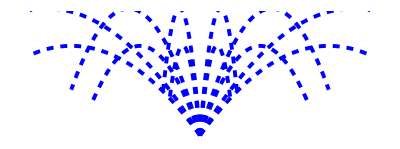

```mathematica
parP[vx_,vy_]:=(
ParametricPlot[{vx t,vy  t-1/2 10 t^2},{t,0,vy/10*9/5},PlotStyle->{Blue,Dashed,Thickness[0.007]}]
)
Show[Table[parP[vx,vy],{vx,{-1.5,-0.7,-0.2,0.7,0.2,1.5}},{vy,{2.1,2.5}}],PlotRange->{{-0.4,0.4},{0,0.3}},Axes->False]
```